# Marcus rate expression for Onodera^2 solvent

## Numerical integration of the flux

## Constants

### Unit conversions

```mathematica
au2kcal=627.5095`30;
kcal2au=1/au2kcal;
ev2cm=8065.54477`30;
cm2ev = 1/ev2cm ;
au2ev=27.2113`30;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;
au2cm=1/cm2au;
au2ps=2.4189`30 10^-5;
fs2ps=10^-3;
ps2au=1/au2ps;
```

### Universal constants

```mathematica
hbar=1;
kb=3.16683`30 10^-6;
```

## Parameters

```mathematica
eps0=79.0`30;
epsi=1.476`30;
eps1=77.58550035542439`30;
tauO=0.006673932065035718`30;
tau1=0.07723670714772116`30;
tau2=11.829849858911379`30;
```

## Spectral density for Onodera^2 dielectric function and ω-integral

```mathematica
J[ω_,ϵi_,ϵ0_,ϵ1_,τO_,τ1_,τ2_]:=Module[{imϵO2,reϵO2,ϵO2abs2},
imϵO2=((ϵ1-ϵi)ω (τ2+τO))/((1+ ω^2 τ2^2)(1+ω^2 τO^2)) + ((ϵ0-ϵ1) ω (τ1+τO))/((1+ ω^2 τ1^2)(1+ω^2 τO^2));
reϵO2=ϵi+((ϵ1-ϵi) (1 -ω^2 τ2 τO))/((1+ ω^2 τ2^2)(1+ω^2 τO^2)) + ((ϵ0-ϵ1) (1-ω^2 τ1 τO))/((1+ ω^2 τ1^2)(1+ω^2 τO^2));
ϵO2abs2=(reϵO2)^2+(imϵO2)^2;
imϵO2/ϵO2abs2
];
```

```mathematica
Iω[ω_,ϵi_,ϵ0_,ϵ1_,τO_,τ1_,τ2_]:=Module[{},
1/ω J[ω,ϵi,ϵ0,ϵ1,τO,τ1,τ2]
];
```

```mathematica
Manipulate[Plot[Iω[ω,epsi,eps0,eps1,τO,τ1,tau2],{ω,-50,50},PlotRange->{0,0.15}],{τO,0,0.5},{τ1,0,tau2}]
```

```mathematica
NIntegrate[Iω[ω,epsi,eps0,eps1,tauO,tau1,tau2],{ω,-∞,∞},WorkingPrecision->20,AccuracyGoal->∞]
```

2.0886833116950973426

```mathematica
Manipulate[NIntegrate[Iω[ω,epsi,eps0,eps1,τO,τ1,tau2],{ω,-∞,∞},WorkingPrecision->$MachinePrecision],{τO,0,0.5`30},{τ1,0,tau2}]
```

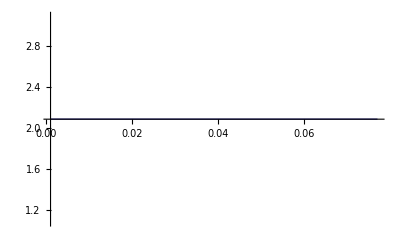

```mathematica
ListLinePlot[Table[{τO,NIntegrate[Iω[ω,epsi,eps0,eps1,τO,tau1,tau2],{ω,-∞,∞},WorkingPrecision->20]},{τO,0.001`30,tau1,0.001`30}],PlotRange->All]
```

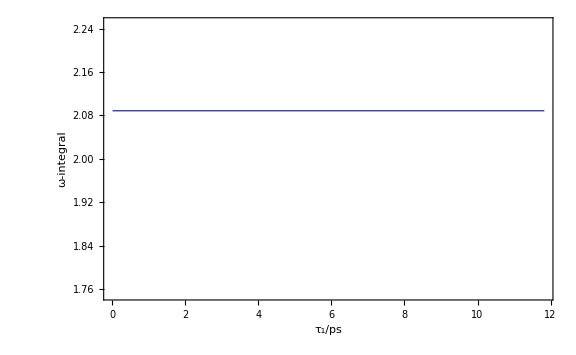

```mathematica
ListLinePlot[Table[{τ1,NIntegrate[Iω[ω,epsi,eps0,eps1,tauO,τ1,tau2],{ω,-∞,∞},WorkingPrecision->20,AccuracyGoal->∞]},{τ1,tauO,tau2,0.002`30}],PlotRange->{1.75,2.25},Axes->False,Frame->True,FrameLabel->{"τ_1/ps","ω-integral"},ImageSize->Large]
```

## Flux

```mathematica
flux[t_,G_,λ_,T_,ϵi_,ϵ0_,ϵ1_,τO_,τ1_,τ2_]:=Module[{β,prefactor,z1,z2,hbar,f0,FI,term1,term2},
β = 1/(kb T au2kcal);
hbar = au2kcal au2ps;
f0 =  (4 π ϵ0 ϵi)/(ϵ0-ϵi);
prefactor=-(f0 λ)/(4 π^2 β hbar^2);
FI=NIntegrate[Iω[ω,ϵi,ϵ0,ϵ1,τO,τ1,τ2],{ω,-∞,∞},MinRecursion->10,MaxRecursion->20,WorkingPrecision->20,AccuracyGoal->∞];
Exp[-ⅈ/hbar(G+λ)t+ⅈ/hbar λ Abs[t]]*Exp[prefactor*FI*(t^2+ⅈ Abs[t] β hbar)]
];
```

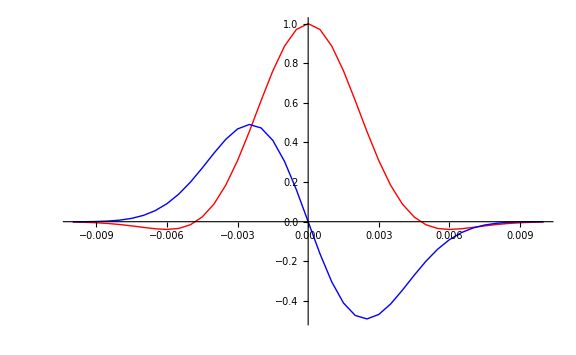

```mathematica
λ=25.0`30;
dG=-20.0`30;
Temp=298.0`30;
ListLinePlot[
{Table[{t,Re[flux[t,dG,λ,Temp,epsi,eps0,eps1,tauO,tau1,tau2]]},{t,-0.01,0.01,0.0005}],
Table[{t,Im[flux[t,dG,λ,Temp,epsi,eps0,eps1,tauO,tau1,tau2]]},{t,-0.01,0.01,0.0005}]},
PlotRange->All,PlotStyle->{Red,Blue},ImageSize->Large]
```

## Nonadiabatic rate

```mathematica
Marcusrate[V_,G_,λ_,T_]:=Module[{β,hbar},
β=1/(kb T au2kcal);
hbar=au2kcal au2ps;
(2π)/hbar V^2 √(β/(4π λ))Exp[-β(G+λ)^2/(4λ)]
];
```

```mathematica
rateOnodera2[V_,G_,λ_,T_,ϵi_,ϵ0_,ϵ1_,τO_,τ1_,τ2_] := Module[{β,hbar,integral},
β = 1/(kb T au2kcal);
hbar = au2kcal au2ps;
integral =2 NIntegrate[Re[flux[t,G,λ,T,ϵi,ϵ0,ϵ1,τO,τ1,τ2]],{t,0,∞},WorkingPrecision->20];
V^2/hbar^2 integral 
];
```

```mathematica
eps0=79.0`30;
epsi=1.476`30;
eps1=77.58550035542439`30;
tauO=0.006673932065035718`30;
tau1=0.07723670714772116`30;
tau2=11.829849858911379`30;
V=0.1`30;
Er=25.0`30;
dG=-20.0`30;
Temp=298.0`30;
rateOnodera2[V,dG,Er,Temp,epsi,eps0,eps1,tauO,tau1,tau2]
Marcusrate[V,dG,Er,Temp]
```

0.1989727559441213993

0.1989727559441213993461224477

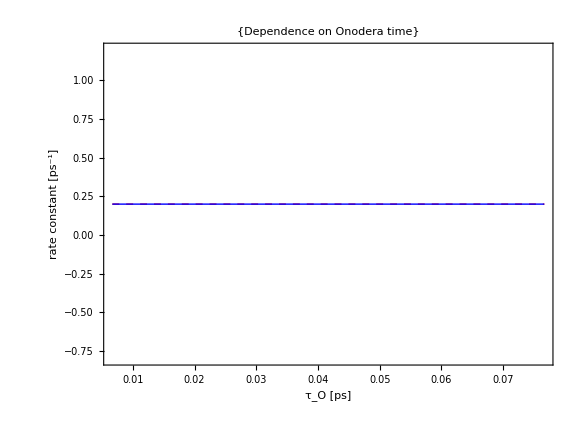

```mathematica
eps0=79.0`30;
epsi=1.476`30;
eps1=77.58550035542439`30;
tauO=0.006673932065035718`30;
tau1=0.07723670714772116`30;
tau2=11.829849858911379`30;
V=0.1`30;
Er=25.0`30;
dG=-20.0`30;
Temp=298.0`30;
ListLinePlot[{Table[{τO,Marcusrate[V,dG,Er,Temp]},{τO,tauO,tau1,0.005`30}],Table[{τO,rateOnodera2[V,dG,Er,Temp,epsi,eps0,eps1,τO,tau1,tau2]},{τO,tauO,tau1,0.005`30}]},PlotRange->All,PlotStyle->{{Red,Thick,Dashed},{Blue,Thick}},Axes->False,Frame->True,BaseStyle->{FontSize->24},FrameStyle->Thickness[0.0018],FrameLabel->{"τ_O [ps]","rate constant [ps^-1]"},AspectRatio->0.75,ImageSize->Large,PlotLabel->"Dependence on Onodera time"]
```

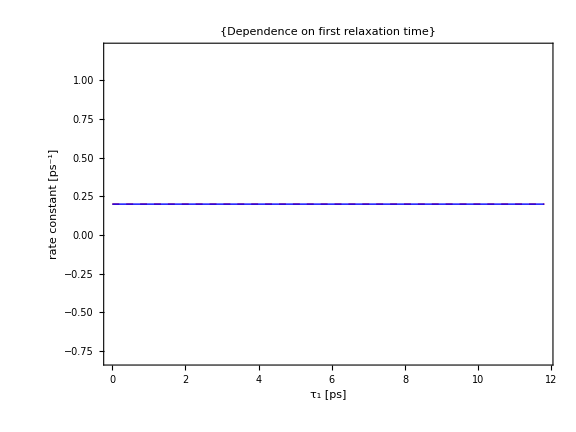

```mathematica
eps0=79.0`30;
epsi=1.476`30;
eps1=77.58550035542439`30;
tauO=0.006673932065035718`30;
tau1=0.07723670714772116`30;
tau2=11.829849858911379`30;
V=0.1`30;
Er=25.0`30;
dG=-20.0`30;
Temp=298.0`30;
ListLinePlot[{Table[{τ1,Marcusrate[V,dG,Er,Temp]},{τ1,tauO,tau2,0.1`30}],Table[{τ1,rateOnodera2[V,dG,Er,Temp,epsi,eps0,eps1,tauO,τ1,tau2]},{τ1,tauO,tau2,0.1`30}]},PlotRange->All,PlotStyle->{{Red,Thick,Dashed},{Blue,Thick}},Axes->False,Frame->True,BaseStyle->{FontSize->24},FrameStyle->Thickness[0.0018],FrameLabel->{"τ_1 [ps]","rate constant [ps^-1]"},AspectRatio->0.75,ImageSize->Large,PlotLabel->"Dependence on first relaxation time"]
```